```mathematica
SetDirectory[DirectoryName[ToFileName["FileName"/.NotebookInformation[SelectedNotebook[]]]]]
```

/home/tbjc1magic/Geant4/tbjc

```mathematica
rawlist=Import["lalal2.dat"];
```

```mathematica
datalist=Transpose[rawlist][[1]];
```

```mathematica
startpoint=330;stoppoint=375;step=0.5;
```

```mathematica
densitylist=BinCounts[datalist,{startpoint,stoppoint,step}]/Length[datalist];
```

```mathematica
Length[densitylist]
```

90

```mathematica
binposition=Table[startpoint+step*(i+0.5),{i,1,(stoppoint-startpoint)/step}];
```

```mathematica
data=Transpose[{binposition,densitylist}];
```

```mathematica
fitpar=FindFit[data,a Exp[-(x-b)^2/(2 c^2)]+d,{a,{b,360},c,d},x]
```

{a→0.0467727,b→357.752,c→4.25105,d→0.0000357171}

```mathematica
a1=a/.fitpar[[1]];b1=b/.fitpar[[2]];
```

```mathematica
c1=c/.fitpar[[3]];
```

```mathematica
d1=d/.fitpar[[4]];
```

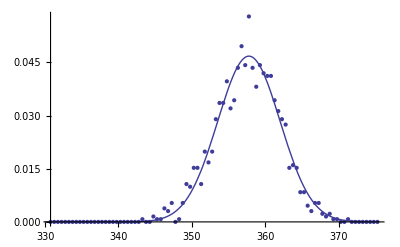

```mathematica
Show[ListPlot[data],Plot[a1 Exp[-(x-b1)^2/(2 c1^2)],{x,startpoint,stoppoint}]]
```